{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>],z→InterpolatingFunction[{{0., 1000.}}, <>]}}

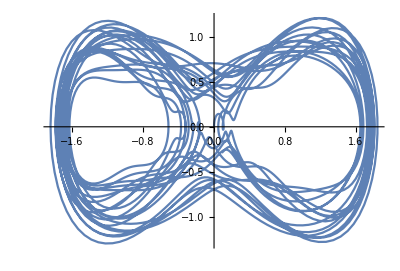

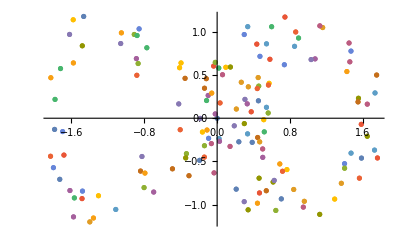

```mathematica
Fx[x_,y_,z_]:=y
Fy[x_,y_,z_]:=x-0.7x^3+0.4*Cos[z]
Fz[x_,y_,z_]:=3
sol=NDSolve[{x'[t]==Fx[x[t],y[t],z[t]],y'[t]==Fy[x[t],y[t],z[t]],z'[t]==Fz[x[t],y[t],z[t]],x[0]==0,y[0]==0,z[0]==0},{x,y,z},{t,0,1000}]
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotRange->All]
ListPlot[Table[Evaluate[{x[2Pi*i],y[2Pi*i]}/.sol],{i,0,150}]]
```